## Signals

```mathematica
SmoothStep[t_,t0_,sig_]:=Piecewise[{{(1+Tanh[(t-t0)/sig])/2,sig>0},{HeavisideTheta[t-t0],sig≤0}}]
SmoothSquare[t_,t0_,t1_,sig1_, sig2_]:=SmoothStep[t,t0,sig1](1-SmoothStep[t,t1,sig2])
ExpStep[t_,t0_,sig_]:=Piecewise[{{0,t≤t0},{1-Exp[-(t-t0)/sig],t>t0}}]
ExpSquare[t_,t0_,t1_,sig1_, sig2_]:=ExpStep[t,t0,sig1](1-ExpStep[t,t1,sig2])
TanhExpSquare[t_,t0_,t1_,sig1_, sig2_]:=SmoothStep[t,t0,sig1](1-ExpStep[t,t1,sig2])
```

```mathematica
Manipulate[Plot[{ExpSquare[t,0.2,0.6,sig1,sig2],SmoothSquare[t,0.2,0.6,sig1,sig2],TanhExpSquare[t,0.2,0.6,sig1,sig2]},{t,0,1.5},PlotStyle->{Blue,Red,Green}],
{{sig1,0.02},0.005,0.1},
{{sig2,0.0394},0.005,0.1}]
```

## Equations

Assumptions
1) neglect neck of pasteur pipette (radius is very small hence volume and surface are very small as well so barely contribute to retardation. 
2) radius therefore is same throughout delivery system 0.55/2 cm
3) Assume concentration at source does not change (volume big enough) during puff. Then define c0 = cs γ(x0) x0 is initial concentration of odorant in gas phase, which is a functoin of saturated vapor concentration (cs), activity coefficient (γ, which is a funciton of x) and x the molar ratio of odorant. x(t=0) = x0.  Here x = n/(n+np) where n = # moles of odorant and np is for paraffin oil. Anyway a bit arbitrary because np is not known since molecular weight of parafin oil is not known (400 g/mol?). We will use c0 as the scaling factor for concentratio nof odorant. It is proportional to the Henry law conefficeint, ie.e. to cs*γ = Ps/(R T)γ where Ps is saturate vapor pressure and T is temperature.
4) as unit of concentration we will use c0
5) parameters: 
             q1→Q1/(π R^2 L1),q2→Q2/(π R^2 L2),qa→ka c0 ,qd→kd, qs→(μ As)/(λ π R^2 L1),W->(2w)/(R c0)

```mathematica
parDef={q1->Q1/(π R^2 L1),q2->Q2/(π R^2 L2),qa->ka c0 ,qd->kd, qs->(μ As)/(λ π R^2 L1),W->(2w)/(R c0), L12->L1/L2};
```

```mathematica
const={Q1->33,Q2->300,R->0.275,L1->(2+2.75)/(π 0.275^2),L2->9};
parKnown={q1->Q1/(π R^2 L1),q2->Q2/(π R^2 L2), L12->L1/L2}/.const
```

{q1→6.94737,q2→140.302,L12→2.22145}

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

```mathematica
normalizeInterpolationFunction[f_]:=f[#]/Max[InterpolatingFunctionValuesOnGrid[f]]&
```

```mathematica
model[qa_?NumberQ,qd_?NumberQ,W_?NumberQ,qs_?NumberQ,T_?NumberQ,t0_?NumberQ,t1_?NumberQ,sig1_?NumberQ,sig2_?NumberQ]:=(model[qa,qd,W,qs,T,t0,t1,sig1,sig2]=normalizeInterpolationFunction[First[f2/.NDSolve[{
c1'[t]==-q q1 c1[t]+qd W θ1[t]-qa W c1[t](1- θ1[t])+qs (1-c1[t]),
θ1'[t]==-qd θ1[t]+qa c1[t](1- θ1[t]),
c2'[t]==-(q q1 L12+ q2)c2[t]+qd W θ2[t]-qa W c2[t](1- θ2[t]) + q q1 L12 c1[t],
θ2'[t]==-qd θ2[t]+qa c2[t](1- θ2[t]),
c1[0]==1,θ1[0]==1/(qd/qa+1),c2[0]==0,θ2[0]==0,f2[t]==(q q1 L12+ q2) c2[t]}/.parKnown/.q->ExpSquare[t,t0,t1,sig1,sig2],{c1,θ1,c2,θ2,f2},{t,0,T}]]]);
```

```mathematica
Manipulate[
Plot[Evaluate[model[10^logqa,10^logqd,10^logW,10^logqs,T,t0,t0+tw,sig1,sig2][t]],{t,0,T},PlotRange->All],
{{logqa,-1},-5,5},
{{logqd,-1},-5,5},
{{logW,0},-5,5},
{{logqs,2},-5,5},
{{T,2.15},0.25,40},
{{t0,0.084},0,1},
{{tw,0.48},0.1,30},
{{sig1,0.01},0.001,0.1},
{{sig2,0.0394},0.001,0.1},ControlPlacement->Left]
```

## data

data from Carlotta, averaged over multiple trials

```mathematica
dat=Import["C:\\Users\\te63\\docs\\projects\\odor_dynamics\\puffs\\data-from-carlotta\\2011_01_10_allPID_sofar\\allPIDsofar_shifted.txt","Table"]//Transpose;
sz=Dimensions[dat];
no=sz[[1]];
nt=sz[[2]];
```

Find time index position of end of puff: tEnd and the amount of the shift needed for some of the traces.

```mathematica
iEnd=Max[Position[dat[[#,All]],x_?(#>0.97&)]]&/@Range[no];
tEnd=Min[iEnd];
tShift=iEnd-tEnd;
```

Make new arrays of data of same dimensions. data1 contain data aligned to onset of puff. data2 contains data aligned to end of puff

```mathematica
data2=Take[dat[[#,All]],{1+tShift[[#]],nt-Max[tShift]+tShift[[#]]}]&/@Range[no];
data1 = Drop[dat[[#,All]],-Max[tShift]]&/@Range[no];
sz=Dimensions[data2];
no=sz[[1]];
nt=sz[[2]];
```

```mathematica
tEnd
tStart=tEnd-50-1
T0=tStart-10
T1=tEnd+70
```

148

97

87

218

Normalize data avoiding the point at tEnd that is always amove the plateau

```mathematica
data3=#/Max[Drop[#,{tEnd}]]&/@data2;
```

```mathematica
Dimensions[data3]
```

{27,1097}

```mathematica
Export["C:\\Users\\te63\\docs\\projects\\odor_dynamics\\matlab\\pid.mat",data3[[All,Range[T0,T1]]],"MAT"]
```

C:\Users\te63\docs\projects\odor_dynamics\matlab\pid.mat

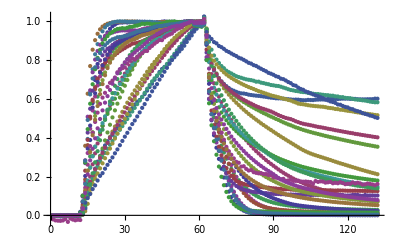

```mathematica
ListPlot[data3[[All,Range[T0,T1]]]]
```

```mathematica
Manipulate[Module[{p1,p2,p11,p22},
p1=ListPlot[data3[[All,Range[it1,it2]]],PlotRange->{{1,it2-it1+1},{-0.09,1.1}},Joined->True,ImageSize->Medium];
p2=ListLogPlot[data3[[All,Range[it1,it2]]],PlotRange->{{1,it2-it1+1},{0.0001,1.1}},Joined->True,ImageSize->Medium];
p11=ListPlot[data3[[oID,Range[it1,it2]]],PlotRange->{{1,it2-it1+1},{-0.09,1.1}},Joined->True,PlotStyle->Thick,ImageSize->Medium];
p22=ListLogPlot[data3[[oID,Range[it1,it2]]],PlotRange->{{1,it2-it1+1},{0.0001,1.1}},Joined->True,PlotStyle->Thick,ImageSize->Medium];
GraphicsRow[{Show[p1,p11],Show[p2,p22]}]],{{oID,1},1,no,1},{{it1,T0},1,nt,1},{{it2,T1},1,nt,1},ControlPlacement->Left]
```

Define the time axis and data vector with time

```mathematica
dt=0.01;
time=(Range[T0,T1]-1)*dt;
d = Transpose[{time,#}]&/@data3[[All,Range[T0,T1]]];
dlog=Transpose[{time,#}]&/@Log[10,data3[[All,Range[T0,T1]]]];
tStart=tStart-T0+1;
T1=T1-T0+1;
tEnd = tEnd-T0+1;
T0 = 1;
```

```mathematica
GraphicsRow[{
ListPlot[d,PlotRange->{All,{-0.09,1.1}},Joined->True,ImageSize->Medium],
ListLogPlot[d,PlotRange->{All,{0.00001,1.1}},Joined->True,ImageSize->Medium],
ListPlot[dlog,PlotRange->{All,{-5,0.1}},Joined->True,ImageSize->Medium]
}]
```

-Graphics-

```mathematica
time
```

{0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2.,2.01,2.02,2.03,2.04,2.05,2.06,2.07,2.08,2.09,2.1,2.11,2.12,2.13,2.14,2.15,2.16,2.17}

```mathematica
time[[tEnd]]-time[[1]]
```

0.61

```mathematica
1.47-time[[0]]
```

## Fitting

Define weights: All 1 apart for the point at tEnd which we weight  with 0.97

```mathematica
w=time 0+1;
```

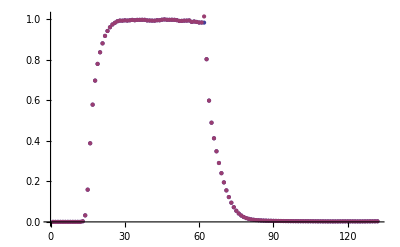

```mathematica
w=time 0+1;
w[[tEnd]]=0.97;
ListPlot[{w d[[1,All,2]],d[[1,All,2]]}]
```

Get older fits

```mathematica
Manipulate[Module[{f,lp,lplog,lpFit,lplogFit},
f=model[10^logqa,10^logqd,10^logW,10^logqs,time[[iT]],t0,t1,sig1,sig2];
lp=ListPlot[d[[oID,Range[iT],All]],PlotRange->{{time[[T0+1]],time[[iT]]},All}];
lplog=ListLogPlot[d[[oID,Range[iT],All]],PlotRange->{{time[[T0+1]],time[[iT]]},{0.001,1.1}}];
lpFit=Plot[fit[t],{t,0,time[[iT]]},PlotRange->{{time[[T0+1]],time[[iT]]},{0,1.1}},PlotStyle->Green];
lplogFit=LogPlot[fit[t],{t,0,time[[iT]]},PlotRange->{{time[[T0+1]],time[[iT]]},{0.001,1.1}},PlotStyle->Green];
GraphicsRow[{
Show[Plot[f[t],{t,0,time[[iT]]},PlotRange->{{time[[T0+1]],time[[iT]]},{0,1.1}},PlotStyle->Red,ImageSize->Medium],lp,lpFit],
Show[LogPlot[f[t],{t,0,time[[iT]]},PlotRange->{{time[[T0+1]],time[[iT]]},{0.001,1.1}},PlotStyle->Red,ImageSize->Medium],lplog,lplogFit]
}]],
Row[{
Button["Save",
pInit=Append[pInit,{oID,logqa,logqd,logW,logqs,iT,t0,t1,sig1,sig2}];
pFit=Append[pFit,{oID,Flogqa,Flogqd,FlogW,Flogqs,iT,t0,t1,sig1,sig2}/.fit["BestFitParameters"]];
fits=Append[fits,fit];],
Button["Reset",pInit={};pFit={};fits={};],
Button["Fit",fit=NonlinearModelFit[
d[[oID,Range[iT],All]],
model[10^Flogqa,10^Flogqd,10^FlogW,10^Flogqs,time[[iT]],t0,t1,sig1,sig2][t],
{{Flogqa,logqa},{Flogqd,logqd},{FlogW,logW},{Flogqs,logqs}},t,WorkingPrecision->3,AccuracyGoal->3,PrecisionGoal->3(*,Weights->w[[Range[iT]]]*)
]]
}],
{{oID,1},1,no,1},
{{logqa,2.6},-5,5},
{{logqd,0.4},-5,5},
{{logW,-1.3},-5,5},
{{logqs,3.34},-4,6},
{{iT,T1},T0+1,T1,1},
{{t0,time[[tStart+2]]},0,1},
{{t1,time[[tEnd]]},0.1,30},
{{sig1,0.025},0.001,0.1},
{{sig2,0.038},0.001,0.1},ControlPlacement->Left,Initialization:>(pInit={};pFit={};fits={})]
```

```mathematica
fit["ParameterTable"]
```

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

| Estimate | Standard Error | t-Statistic | P-Value
Flogqa | 3.28 | 0.0627263 | 52.2249 | 3.59456×10^-88
Flogqd | 1.03 | 0.15873 | 6.51381 | 1.52197×10^-9
FlogW | -0.839 | 0.0232626 | -36.0526 | 6.76849×10^-69
Flogqs | 153. | 0. | ∞ | 0.

```mathematica
pInit;
pFit;
p=(#["ParameterTableEntries"]&)/@fits;
```

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (4).

General::stop: Further output of FittedModel :: precw will be suppressed during this calculation.

```mathematica
Export["C:\\Users\\te63\\docs\\projects\\odor_dynamics\\puffs\\data-from-carlotta\\2011_01_10_allPID_sofar\\fit00_p.dat",p,"Table"]
Export["C:\\Users\\te63\\docs\\projects\\odor_dynamics\\puffs\\data-from-carlotta\\2011_01_10_allPID_sofar\\fit00_p.mat",p,"MAT"]
Export["C:\\Users\\te63\\docs\\projects\\odor_dynamics\\puffs\\data-from-carlotta\\2011_01_10_allPID_sofar\\fit00_pInit.mat",pInit,"MAT"]
Export["C:\\Users\\te63\\docs\\projects\\odor_dynamics\\puffs\\data-from-carlotta\\2011_01_10_allPID_sofar\\fit00_pFit.mat",pFit,"MAT"]
```

C:\Users\te63\docs\projects\odor_dynamics\puffs\data-from-carlotta\2011_01_10_allPID_sofar\fit00_p.dat

C:\Users\te63\docs\projects\odor_dynamics\puffs\data-from-carlotta\2011_01_10_allPID_sofar\fit00_p.mat

C:\Users\te63\docs\projects\odor_dynamics\puffs\data-from-carlotta\2011_01_10_allPID_sofar\fit00_pInit.mat

C:\Users\te63\docs\projects\odor_dynamics\puffs\data-from-carlotta\2011_01_10_allPID_sofar\fit00_pInit.mat

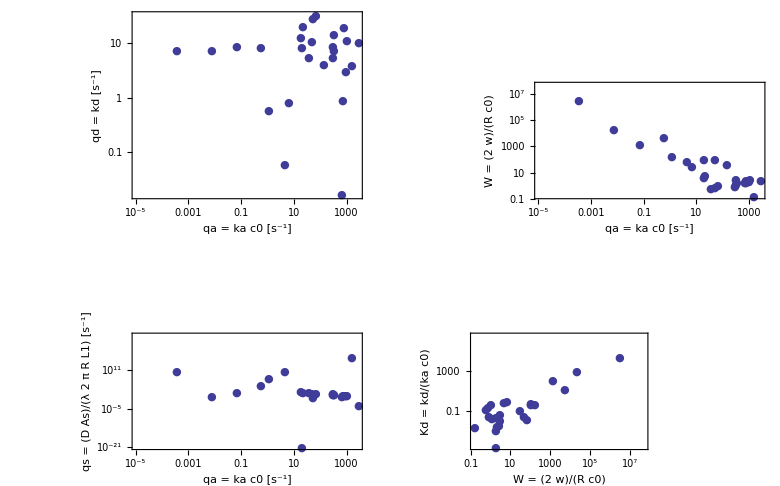

```mathematica
GraphicsGrid[{{
ListLogLogPlot[10.^pFit[[All,{2,3}]],PlotMarkers->{Automatic,Small},FrameLabel->{"qa = ka c0   [s^-1]","qd = kd   [s^-1]"},Frame->True,ImageSize->Medium],
ListLogLogPlot[10.^pFit[[All,{2,4}]],PlotMarkers->{Automatic,Small},FrameLabel->{"qa = ka c0   [s^-1]","W = (2  w)/(R c0)"},Frame->True,ImageSize->Medium]},{
ListLogLogPlot[10.^pFit[[All,{2,5}]],PlotMarkers->{Automatic,Small},FrameLabel->{"qa = ka c0   [s^-1]","qs = (D As)/(λ 2  π R L1)  [s^-1]"},Frame->True,ImageSize->Medium],
ListLogLogPlot[10.^Transpose[{pFit[[All,4]],pFit[[All,3]]-pFit[[All,2]]}],PlotMarkers->{Automatic,Small},FrameLabel->{"W = (2  w)/(R c0)","Kd = kd/(ka c0)"},Frame->True,ImageSize->Medium]}}]
```

```mathematica
Series[1/(x+dx),{dx,0,2}]
```

1/x-dx/x^2+dx^2/x^3+O[dx]^3

```mathematica
Needs["ErrorBarPlots`"]
```

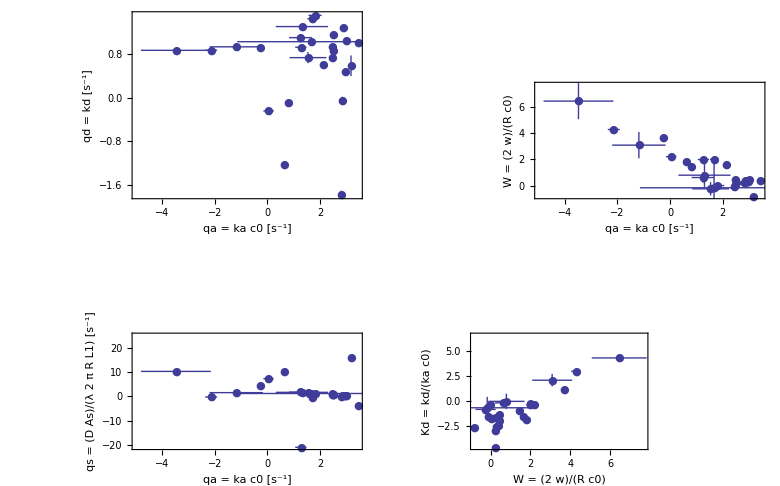

```mathematica
GraphicsGrid[{{
ErrorListPlot[{#[[All,1]],ErrorBar@@#[[All,2]]}&/@p[[All,{1,2},{1,2}]],
ErrorBarFunction->Automatic,PlotMarkers->{Automatic,Small},FrameLabel->{"qa = ka c0   [s^-1]","qd = kd   [s^-1]"},Frame->True,ImageSize->Medium,Axes->None],
ErrorListPlot[{#[[All,1]],ErrorBar@@#[[All,2]]}&/@p[[All,{1,3},{1,2}]],
ErrorBarFunction->Automatic,PlotMarkers->{Automatic,Small},FrameLabel->{"qa = ka c0   [s^-1]","W = (2  w)/(R c0)"},Frame->True,ImageSize->Medium,Axes->None]},{
ErrorListPlot[{#[[All,1]],ErrorBar@@#[[All,2]]}&/@p[[All,{1,4},{1,2}]],
ErrorBarFunction->Automatic,PlotMarkers->{Automatic,Small},FrameLabel->{"qa = ka c0   [s^-1]","qs = (D As)/(λ 2  π R L1)  [s^-1]"},Frame->True,ImageSize->Medium,Axes->None],
ErrorListPlot[{{#[[3,1]],#[[2,1]]-#[[1,1]]},ErrorBar@@{#[[3,2]],#[[2,2]]/#[[1,1]]+#[[1,2]]#[[2,1]]/(#[[1,1]])^2}}&/@p[[All,{1,2,3},{1,2}]],
ErrorBarFunction->Automatic,PlotMarkers->{Automatic,Small},FrameLabel->{"W = (2  w)/(R c0)","Kd = kd/(ka c0)"},Frame->True,ImageSize->Medium,Axes->None]
}}]
```

```mathematica
(#["AdjustedRSquared"]&)/@fits
(#["BIC"]&)/@fits
```

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (4).

General::stop: Further output of FittedModel :: precw will be suppressed during this calculation.

{0.998834,0.999148,0.998733,0.998224,0.999192,0.999574,0.998108,0.998779,0.9997,0.998154,0.999529,0.998134,0.996607,0.999238,0.999533,0.997928,0.99965,0.999231,0.997876,0.996197,0.998472,0.9997,0.998101,0.998729,0.999251,0.999332,0.998973}

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (4).

General::stop: Further output of FittedModel :: precw will be suppressed during this calculation.

{-638.406,-698.276,-645.421,-593.392,-675.544,-775.985,-564.255,-648.187,-811.507,-579.055,-764.124,-566.101,-512.322,-699.498,-771.56,-569.632,-775.459,-699.228,-561.203,-464.862,-610.42,-794.23,-595.416,-639.364,-698.075,-715.826,-672.277}

```mathematica
pRule=Map[{oID->#[[1]],logqa->#[[2]],logqd->#[[3]],logW->#[[4]],logqs->#[[5]],iT->#[[6]],t0->#[[7]],t1->#[[8]],sig1->#[[9]],sig2->#[[10]]}&,pFit];MatrixForm[pRule]
```

(oID→1 | logqa→3.171 | logqd→0.59 | logW→-0.8328 | logqs→15.83 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→2 | logqa→2.486 | logqd→1.171 | logW→0.4405 | logqs→0.8693 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→3 | logqa→3.003 | logqd→1.051 | logW→0.4536 | logqs→0.3329 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→4 | logqa→2.442 | logqd→0.9347 | logW→-0.1021 | logqs→1.338 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→5 | logqa→2.134 | logqd→0.614 | logW→1.636 | logqs→144.8 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→6 | logqa→1.306 | logqd→1.31 | logW→0.7963 | logqs→1.696 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→7 | logqa→1.67 | logqd→1.032 | logW→-0.166 | logqs→1.22 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→8 | logqa→2.967 | logqd→0.481 | logW→0.2816 | logqs→0.1351 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→9 | logqa→1.808 | logqd→1.517 | logW→0.004452 | logqs→1.347 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→10 | logqa→1.538 | logqd→0.7393 | logW→-0.2472 | logqs→1.526 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→11 | logqa→1.253 | logqd→1.107 | logW→0.6166 | logqs→1.795 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→12 | logqa→3.43 | logqd→1.02 | logW→0.371 | logqs→-3.67 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→13 | logqa→-12.5 | logqd→0.856 | logW→14.9 | logqs→9.13 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→14 | logqa→0.0415 | logqd→-0.241 | logW→2.22 | logqs→7.38 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→15 | logqa→0.798 | logqd→-0.0952 | logW→1.47 | logqs→36.1 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→16 | logqa→-2.14 | logqd→0.875 | logW→4.29 | logqs→-0.24 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→17 | logqa→-0.273 | logqd→0.921 | logW→3.71 | logqs→4.31 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→18 | logqa→-1.18 | logqd→0.938 | logW→3.1 | logqs→1.57 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→19 | logqa→-3.48 | logqd→0.874 | logW→6.46 | logqs→10.3 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→20 | logqa→1.27 | logqd→0.929 | logW→2. | logqs→-21. | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→21 | logqa→2.86 | logqd→1.29 | logW→0.39 | logqs→0.51 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→22 | logqa→1.69 | logqd→1.46 | logW→2.01 | logqs→-0.348 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→23 | logqa→2.84 | logqd→-0.0481 | logW→0.252 | logqs→0.163 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→24 | logqa→2.46 | logqd→0.748 | logW→0.057 | logqs→0.948 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→25 | logqa→0.618 | logqd→-1.22 | logW→1.81 | logqs→10.1 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→26 | logqa→2.8 | logqd→-1.79 | logW→0.223 | logqs→0.0506 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038
oID→27 | logqa→2.51 | logqd→0.861 | logW→0.254 | logqs→0.793 | iT→132 | t0→0.98 | t1→1.47 | sig1→0.025 | sig2→0.038)

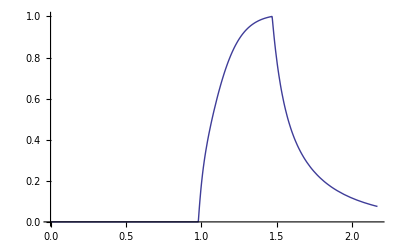

```mathematica
Plot[fits[[2]][t],{t,0,time[[132]]}]
```

```mathematica
(*
fits=NonlinearModelFit[
d[[oID/.#,Range[iT/.#],All]],
model[10^logqa,10^logqd,10^logW,10^logqs,time[[iT/.#]],t0/.#,t1/.#,sig1/.#,sig2/.#][t],
{{logqa,(logqa/.#)},{logqd,(logqd/.#)},{logW,(logW/.#)},{logqs,(logqs/.#)}},t,WorkingPrecision->3,AccuracyGoal->3,PrecisionGoal->3]&/@pRule
*)
```

```mathematica
pl={ListPlot[d[[oID/.#,Range[iT/.#],All]],PlotRange->{{time[[T0+1]],time[[iT/.#]]},All},ImageSize->Small,PlotLabel->(oID/.#)],
Plot[fits[[oID/.#]][t],{t,0,time[[iT/.#]]},PlotStyle->Red]}&/@pRule;
```

```mathematica
GraphicsGrid[Partition[Show[#]&/@pl,5,5,1,{}]]
```

-Graphics-